```mathematica
Clear[su,pr,r,s,q]
(* range of u in plot  *)
plo[r_,s_,t_]:={-t/(s+t)-(t+r)/(s+t)u,t/(t-s)+(r-t)/(t-s)u,t/(t-s)+(t+r)/(t-s)u,-t/(s+t)-(r-t)/(s+t)u}
(* range of u in plot  *)

su[r_,s_,t_]:={u,-t/(t+r),t/(t-r)};
(* Plot Range *)
pr[r_,s_,t_]:={{-t/(t+r),t/(t-r)},{-t/(s+t),t/(t-s)}}
```

```mathematica
(1,1,3)  Case σ=τ,Evolution (σ,σ) for σ in [0,1/2]
```

```mathematica
curve=6561+17496 u-34992 u^2-132192 u^3-33696 u^4+217728 u^5+269568 u^6+124416 u^7+20736 u^8+17496 v+34992 u v-116640 u^2 v-274752 u^3 v+93312 u^4 v+518400 u^5 v+373248 u^6 v+82944 u^7 v-34992 v^2-46656 u v^2+264384 u^2 v^2+373248 u^3 v^2-435456 u^4 v^2-746496 u^5 v^2-248832 u^6 v^2-62208 v^3-41472 u v^3+497664 u^2 v^3+331776 u^3 v^3-995328 u^4 v^3-663552 u^5 v^3+82944 v^4-663552 u^2 v^4+1327104 u^4 v^4-78732 σ-288684 u σ-64152 u^2 σ+431568 u^3 σ-702432 u^4 σ-1982016 u^5 σ-637056 u^6 σ+624384 u^7 σ+299520 u^8 σ-131220 v σ-705672 u v σ-1271376 u^2 v σ-438048 u^3 v σ+986688 u^4 v σ-667008 u^5 v σ-3518208 u^6 v σ-1783296 u^7 v σ+303264 v^2 σ+886464 u v^2 σ-62208 u^2 v^2 σ-898560 u^3 v^2 σ+1866240 u^4 v^2 σ+3566592 u^5 v^2 σ+2433024 u^6 v^2 σ+699840 v^3 σ+2788992 u v^3 σ+2916864 u^2 v^3 σ+1207296 u^3 v^3 σ+3087360 u^4 v^3 σ+2451456 u^5 v^3 σ-663552 v^4 σ-1548288 u v^4 σ+442368 u^2 v^4 σ-884736 u^3 v^4 σ-5308416 u^4 v^4 σ-774144 v^5 σ-3317760 u v^5 σ-3981312 u^2 v^5 σ-884736 u^3 v^5 σ+589824 v^6 σ+2359296 u v^6 σ+2359296 u^2 v^6 σ+314928 σ^2+1548396 u σ^2+2026620 u^2 σ^2+23328 u^3 σ^2+244944 u^4 σ^2+2655936 u^5 σ^2+793152 u^6 σ^2-1419264 u^7 σ^2-656640 u^8 σ^2+131220 v σ^2+2006208 u v σ^2+7406640 u^2 v σ^2+8320320 u^3 v σ^2-3329856 u^4 v σ^2-6289920 u^5 v σ^2+6296832 u^6 v σ^2+5170176 u^7 v σ^2-1280124 v^2 σ^2-5727024 u v^2 σ^2-7103376 u^2 v^2 σ^2-1683072 u^3 v^2 σ^2+603072 u^4 v^2 σ^2+601344 u^5 v^2 σ^2-587520 u^6 v^2 σ^2-1143072 v^3 σ^2-8164800 u v^3 σ^2-16084224 u^2 v^3 σ^2-12510720 u^3 v^3 σ^2-6584832 u^4 v^3 σ^2-4230144 u^5 v^3 σ^2+1975104 v^4 σ^2+8847360 u v^4 σ^2+10630656 u^2 v^4 σ^2+7520256 u^3 v^4 σ^2+8156160 u^4 v^4 σ^2+1520640 v^5 σ^2+9234432 u v^5 σ^2+8957952 u^2 v^5 σ^2+221184 u^3 v^5 σ^2-1437696 v^6 σ^2-8110080 u v^6 σ^2-5750784 u^2 v^6 σ^2-262440 σ^3-2589408 u σ^3-6852600 u^2 σ^3-4090176 u^3 σ^3+7177248 u^4 σ^3+7105536 u^5 σ^3-4475520 u^6 σ^3-2909184 u^7 σ^3+2756096 u^8 σ^3+1189728 v σ^3+2881008 u v σ^3-4548960 u^2 v σ^3-16765056 u^3 v σ^3-5011200 u^4 v σ^3+10651392 u^5 v σ^3-222720 u^6 v σ^3-3313664 u^7 v σ^3+1965384 v^2 σ^3+12830400 u v^2 σ^3+19152288 u^2 v^2 σ^3+2958336 u^3 v^2 σ^3-3839616 u^4 v^2 σ^3-2423808 u^5 v^2 σ^3-7787008 u^6 v^2 σ^3-3506976 v^3 σ^3-6422976 u v^3 σ^3+1195776 u^2 v^3 σ^3+7838208 u^3 v^3 σ^3-35328 u^4 v^3 σ^3+1586176 u^5 v^3 σ^3-1648512 v^4 σ^3-15026688 u v^4 σ^3-16533504 u^2 v^4 σ^3+780288 u^3 v^4 σ^3+7804928 u^4 v^4 σ^3+5571072 v^5 σ^3+5833728 u v^5 σ^3+5289984 u^2 v^5 σ^3+6516736 u^3 v^5 σ^3-1216512 v^6 σ^3+5652480 u v^6 σ^3-2179072 u^2 v^6 σ^3-3932160 v^7 σ^3-2097152 u v^7 σ^3+2097152 v^8 σ^3-1338444 σ^4-3569184 u σ^4+2452356 u^2 σ^4+10532592 u^3 σ^4-6776784 u^4 σ^4-20525184 u^5 σ^4+4473792 u^6 σ^4+10513152 u^7 σ^4-3819264 u^8 σ^4-3569184 v σ^4-17455176 u v σ^4-23351328 u^2 v σ^4+7270560 u^3 v σ^4+25522560 u^4 v σ^4-2443392 u^5 v σ^4-14920704 u^6 v σ^4-4781568 u^7 v σ^4+2452356 v^2 σ^4-3347568 u v^2 σ^4-12888720 u^2 v^2 σ^4+3393792 u^3 v^2 σ^4+2096064 u^4 v^2 σ^4-15061248 u^5 v^2 σ^4+6963456 u^6 v^2 σ^4+10380960 v^3 σ^4+40357440 u v^3 σ^4+53129088 u^2 v^3 σ^4+27862272 u^3 v^3 σ^4+15482880 u^4 v^3 σ^4+1554432 u^5 v^3 σ^4-7029504 v^4 σ^4+141696 u v^4 σ^4-2847744 u^2 v^4 σ^4-23910912 u^3 v^4 σ^4-25073664 u^4 v^4 σ^4-15019776 v^5 σ^4-36799488 u v^5 σ^4-25740288 u^2 v^5 σ^4-10776576 u^3 v^5 σ^4+10091520 v^6 σ^4+11169792 u v^6 σ^4+18001920 u^2 v^6 σ^4+7888896 v^7 σ^4+4964352 u v^7 σ^4-5111808 v^8 σ^4+3149280 σ^5+15326496 u σ^5+20703600 u^2 σ^5-6881760 u^3 σ^5-23950080 u^4 σ^5+7098624 u^5 σ^5+15572736 u^6 σ^5-4603392 u^7 σ^5-3532800 u^8 σ^5+1469664 v σ^5+19152288 u v σ^5+45606240 u^2 v σ^5+19051200 u^3 v σ^5-21862656 u^4 v σ^5+4631040 u^5 v σ^5+21321216 u^6 v σ^5+2638848 u^7 v σ^5-11629008 v^2 σ^5-29229984 u v^2 σ^5-12877056 u^2 v^2 σ^5+3739392 u^3 v^2 σ^5-7596288 u^4 v^2 σ^5+18178560 u^5 v^2 σ^5+13737984 u^6 v^2 σ^5-1096416 v^3 σ^5-24183360 u v^3 σ^5-36695808 u^2 v^3 σ^5-20915712 u^3 v^3 σ^5-15469056 u^4 v^3 σ^5+1754112 u^5 v^3 σ^5+21617280 v^4 σ^5+30951936 u v^4 σ^5+6994944 u^2 v^4 σ^5+2608128 u^3 v^4 σ^5-6610944 u^4 v^4 σ^5-428544 v^5 σ^5+15856128 u v^5 σ^5-7160832 u^2 v^5 σ^5-2936832 u^3 v^5 σ^5-15399936 v^6 σ^5-14764032 u v^6 σ^5-5578752 u^2 v^6 σ^5+2727936 v^7 σ^5-1867776 u v^7 σ^5+1572864 v^8 σ^5-8188128 u σ^6-28215216 u^2 σ^6-15139872 u^3 σ^6+34271424 u^4 σ^6+23390208 u^5 σ^6-22823424 u^6 σ^6-9159168 u^7 σ^6+9072640 u^8 σ^6+8188128 v σ^6+12013920 u v σ^6-28063584 u^2 v σ^6-53037504 u^3 v σ^6-8771328 u^4 v σ^6+2944512 u^5 v σ^6-8348160 u^6 v σ^6+4502528 u^7 v σ^6+9996048 v^2 σ^6+39680928 u v^2 σ^6+16765056 u^2 v^2 σ^6-35209728 u^3 v^2 σ^6+12358656 u^4 v^2 σ^6+11284992 u^5 v^2 σ^6-25874432 u^6 v^2 σ^6-21298464 v^3 σ^6-35308224 u v^3 σ^6-36702720 u^2 v^3 σ^6-28643328 u^3 v^3 σ^6+7306752 u^4 v^3 σ^6-904192 u^5 v^3 σ^6-18449856 v^4 σ^6-42550272 u v^4 σ^6+3628800 u^2 v^4 σ^6+22333440 u^3 v^4 σ^6+45942784 u^4 v^4 σ^6+24696576 v^5 σ^6+24551424 u v^5 σ^6+40522752 u^2 v^5 σ^6+11620352 u^3 v^5 σ^6+5688576 v^6 σ^6+872448 u v^6 σ^6-20455424 u^2 v^6 σ^6-14149632 v^7 σ^6-1662976 u v^7 σ^6+4870144 v^8 σ^6-6298560 σ^7-19315584 u σ^7-4618944 u^2 σ^7+31352832 u^3 σ^7+13156992 u^4 σ^7-25754112 u^5 σ^7-7147008 u^6 σ^7+9142272 u^7 σ^7-1363968 u^8 σ^7-14276736 v σ^7-47869056 u v σ^7-22208256 u^2 v σ^7+57604608 u^3 v σ^7+25132032 u^4 v σ^7-33481728 u^5 v σ^7-6875136 u^6 v σ^7+884736 u^7 v σ^7+7138368 v^2 σ^7-7464960 u v^2 σ^7-373248 u^2 v^2 σ^7+49144320 u^3 v^2 σ^7-3138048 u^4 v^2 σ^7-40366080 u^5 v^2 σ^7+3465216 u^6 v^2 σ^7+25940736 v^3 σ^7+47029248 u v^3 σ^7+35458560 u^2 v^3 σ^7+39730176 u^3 v^3 σ^7-12791808 u^4 v^3 σ^7-12238848 u^5 v^3 σ^7-8926848 v^4 σ^7+18413568 u v^4 σ^7+1479168 u^2 v^4 σ^7+15446016 u^3 v^4 σ^7-18247680 u^4 v^4 σ^7-18786816 v^5 σ^7-4257792 u v^5 σ^7+2598912 u^2 v^5 σ^7+7372800 u^3 v^5 σ^7+10796544 v^6 σ^7+4276224 u v^6 σ^7+14008320 u^2 v^6 σ^7+5566464 v^7 σ^7-2211840 u v^7 σ^7-4055040 v^8 σ^7+5353776 σ^8+24354432 u σ^8+30058128 u^2 σ^8-12807072 u^3 σ^8-38382336 u^4 σ^8+3545856 u^5 σ^8+22394880 u^6 σ^8-1082880 u^7 σ^8-5630976 u^8 σ^8+4199040 v σ^8+40800672 u v σ^8+64688544 u^2 v σ^8-1975104 u^3 v σ^8-17076096 u^4 v σ^8+31760640 u^5 v σ^8+10469376 u^6 v σ^8-5529600 u^7 v σ^8-16971120 v^2 σ^8-8561376 u v^2 σ^8+28180224 u^2 v^2 σ^8-4883328 u^3 v^2 σ^8-6815232 u^4 v^2 σ^8+31408128 u^5 v^2 σ^8+16054272 u^6 v^2 σ^8-5435424 v^3 σ^8-7262784 u v^3 σ^8+22301568 u^2 v^3 σ^8-12116736 u^3 v^3 σ^8+8672256 u^4 v^3 σ^8+14008320 u^5 v^3 σ^8+26158464 v^4 σ^8+6811776 u v^4 σ^8-2951424 u^2 v^4 σ^8-39817728 u^3 v^4 σ^8-19491840 u^4 v^4 σ^8+248832 v^5 σ^8-21247488 u v^5 σ^8-34200576 u^2 v^5 σ^8-17768448 u^3 v^5 σ^8-14231808 v^6 σ^8-903168 u v^6 σ^8+4460544 u^2 v^6 σ^8+4663296 v^7 σ^8+4202496 u v^7 σ^8-479232 v^8 σ^8+2099520 σ^9-699840 u σ^9-18242496 u^2 σ^9-17900352 u^3 σ^9+9082368 u^4 σ^9+12040704 u^5 σ^9-3170304 u^6 σ^9-2626560 u^7 σ^9+2764800 u^8 σ^9+11897280 v σ^9+1306368 u v σ^9-57900096 u^2 v σ^9-53903232 u^3 v σ^9+2101248 u^4 v σ^9+4326912 u^5 v σ^9-4008960 u^6 v σ^9+1105920 u^7 v σ^9+11150784 v^2 σ^9-3312576 u v^2 σ^9-67651200 u^2 v^2 σ^9-47056896 u^3 v^2 σ^9+7271424 u^4 v^2 σ^9+2211840 u^5 v^2 σ^9-8847360 u^6 v^2 σ^9-13701312 v^3 σ^9-21244032 u v^3 σ^9-48301056 u^2 v^3 σ^9-10404864 u^3 v^3 σ^9+9123840 u^4 v^3 σ^9-16578432 v^4 σ^9-7229952 u v^4 σ^9-6414336 u^2 v^4 σ^9+11197440 u^3 v^4 σ^9+16035840 u^4 v^4 σ^9+3953664 v^5 σ^9+6815232 u v^5 σ^9+5944320 u^2 v^5 σ^9+3317760 u^3 v^5 σ^9+3050496 v^6 σ^9-1935360 u v^6 σ^9-7741440 u^2 v^6 σ^9-2211840 v^7 σ^9+2211840 v^8 σ^9-5038848 σ^10-12177216 u σ^10-46656 u^2 σ^10+19455552 u^3 σ^10+11606976 u^4 σ^10-9752832 u^5 σ^10-8748288 u^6 σ^10+2350080 u^7 σ^10+663552 u^8 σ^10-14696640 v σ^10-26127360 u v σ^10+14043456 u^2 v σ^10+42166656 u^3 v σ^10+4278528 u^4 v σ^10-18413568 u^5 v σ^10-1022976 u^6 v σ^10+2211840 u^7 v σ^10-5925312 v^2 σ^10-5085504 u v^2 σ^10+35769600 u^2 v^2 σ^10+36509184 u^3 v^2 σ^10-4845312 u^4 v^2 σ^10-16865280 u^5 v^2 σ^10-663552 u^6 v^2 σ^10+10404288 v^3 σ^10+8263296 u v^3 σ^10+22159872 u^2 v^3 σ^10+9197568 u^3 v^3 σ^10-14598144 u^4 v^3 σ^10-7299072 u^5 v^3 σ^10+3053376 v^4 σ^10+670464 u v^4 σ^10+8232192 u^2 v^4 σ^10+10533888 u^3 v^4 σ^10-3207168 u^4 v^4 σ^10+988416 v^5 σ^10+9068544 u v^5 σ^10+15234048 u^2 v^5 σ^10+6635520 u^3 v^5 σ^10+5213952 v^6 σ^10+2211840 u v^6 σ^10+3981312 u^2 v^6 σ^10-1382400 v^7 σ^10-2433024 u v^7 σ^10-1658880 v^8 σ^10+2519424 σ^11+6718464 u σ^11+5412096 u^2 σ^11-1866240 u^3 σ^11-6189696 u^4 σ^11+483840 u^5 σ^11+3608064 u^6 σ^11-995328 u^7 σ^11-663552 u^8 σ^11+6718464 v σ^11+20901888 u v σ^11+19035648 u^2 v σ^11+995328 u^3 v σ^11-2059776 u^4 v σ^11+6552576 u^5 v σ^11+995328 u^6 v σ^11-1327104 u^7 v σ^11+5412096 v^2 σ^11+23514624 u v^2 σ^11+21835008 u^2 v^2 σ^11+4340736 u^3 v^2 σ^11+3359232 u^4 v^2 σ^11+8957952 u^5 v^2 σ^11+1327104 u^6 v^2 σ^11+2612736 v^3 σ^11+15925248 u v^3 σ^11+12303360 u^2 v^3 σ^11+2156544 u^3 v^3 σ^11+6967296 u^4 v^3 σ^11+3981312 u^5 v^3 σ^11+1275264 v^4 σ^11+926208 u v^4 σ^11-2280960 u^2 v^4 σ^11-6967296 u^3 v^4 σ^11-4492800 v^5 σ^11-8709120 u v^5 σ^11-8957952 u^2 v^5 σ^11-3981312 u^3 v^5 σ^11-4686336 v^6 σ^11-995328 u v^6 σ^11-1327104 u^2 v^6 σ^11+995328 v^7 σ^11+1327104 u v^7 σ^11+663552 v^8 σ^11-419904 σ^12-1119744 u σ^12-3732480 u^2 σ^12-5349888 u^3 σ^12+88128 u^4 σ^12+2854656 u^5 σ^12+656640 u^6 σ^12+165888 u^7 σ^12+110592 u^8 σ^12-1119744 v σ^12-9144576 u v σ^12-20155392 u^2 v σ^12-15261696 u^3 v σ^12-76032 u^4 v σ^12+1423872 u^5 v σ^12-165888 u^6 v σ^12+221184 u^7 v σ^12-3732480 v^2 σ^12-20901888 u v^2 σ^12-31943808 u^2 v^2 σ^12-16657920 u^3 v^2 σ^12-1817856 u^4 v^2 σ^12-1492992 u^5 v^2 σ^12-221184 u^6 v^2 σ^12-6096384 v^3 σ^12-17750016 u v^3 σ^12-17985024 u^2 v^3 σ^12-5391360 u^3 v^3 σ^12-1161216 u^4 v^3 σ^12-663552 u^5 v^3 σ^12-1156032 v^4 σ^12-573696 u v^4 σ^12-877824 u^2 v^4 σ^12+1161216 u^3 v^4 σ^12+3684096 v^5 σ^12+3967488 u v^5 σ^12+1492992 u^2 v^5 σ^12+663552 u^3 v^5 σ^12+2039040 v^6 σ^12+165888 u v^6 σ^12+221184 u^2 v^6 σ^12-165888 v^7 σ^12-221184 u v^7 σ^12-110592 v^8 σ^12+1306368 u^2 σ^13+2612736 u^3 σ^13+435456 u^4 σ^13-1354752 u^5 σ^13-580608 u^6 σ^13+2612736 u v σ^13+7838208 u^2 v σ^13+6967296 u^3 v σ^13+193536 u^4 v σ^13-1161216 u^5 v σ^13+1306368 v^2 σ^13+7838208 u v^2 σ^13+13063680 u^2 v^2 σ^13+7354368 u^3 v^2 σ^13+580608 u^4 v^2 σ^13+2612736 v^3 σ^13+6967296 u v^3 σ^13+7354368 u^2 v^3 σ^13+2322432 u^3 v^3 σ^13+435456 v^4 σ^13+193536 u v^4 σ^13+580608 u^2 v^4 σ^13-1354752 v^5 σ^13-1161216 u v^5 σ^13-580608 v^6 σ^13-186624 u^2 σ^14-373248 u^3 σ^14-62208 u^4 σ^14+193536 u^5 σ^14+82944 u^6 σ^14-373248 u v σ^14-1119744 u^2 v σ^14-995328 u^3 v σ^14-27648 u^4 v σ^14+165888 u^5 v σ^14-186624 v^2 σ^14-1119744 u v^2 σ^14-1866240 u^2 v^2 σ^14-1050624 u^3 v^2 σ^14-82944 u^4 v^2 σ^14-373248 v^3 σ^14-995328 u v^3 σ^14-1050624 u^2 v^3 σ^14-331776 u^3 v^3 σ^14-62208 v^4 σ^14-27648 u v^4 σ^14-82944 u^2 v^4 σ^14+193536 v^5 σ^14+165888 u v^5 σ^14+82944 v^6 σ^14;
plo[1,1,3]
```

{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2}

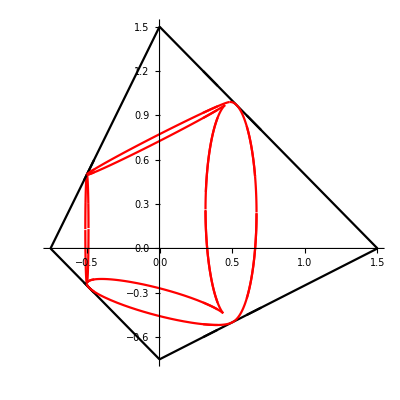

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/32)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/32)==0,v]},{u,-.52,-.45},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/32)==0,v]},{u,.3,.4},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/32)==0,v]},{u,.6,.7},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot1=Show[%,%%,%%%,%%%%](*sigma=1/32*)
```

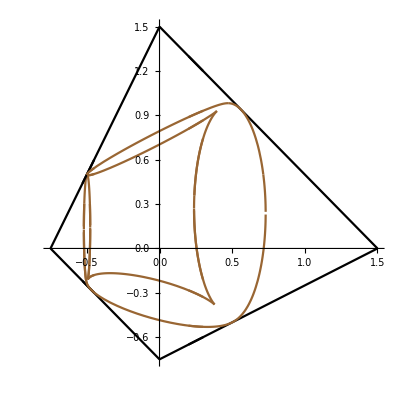

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/16)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Brown}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/16)==0,v]},{u,-.53,-.45},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Brown}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/16)==0,v]},{u,.2,.3},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Brown}];
Plot2=Show[%,%%,%%%]
```

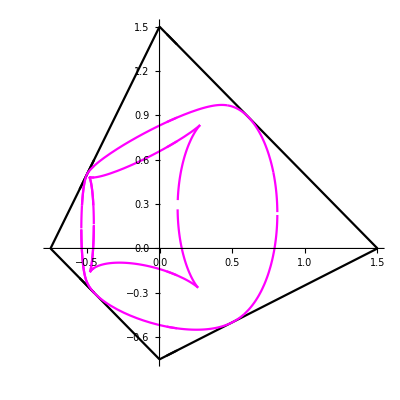

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/8)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/8)==0,v]},{u,-.55,-.45},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/8)==0,v]},{u,.05,.12},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot3=Show[%,%%,%%%]
```

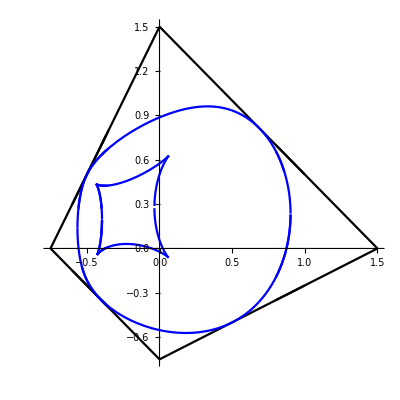

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/4)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Blue}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/4)==0,v]},{u,-.6,-.37},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Blue}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/4)==0,v]},{u,-.4,-.35},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Blue}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/4)==0,v]},{u,.8,1},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Blue}];
Plot4=Show[%,%%,%%%,%%%%]
```

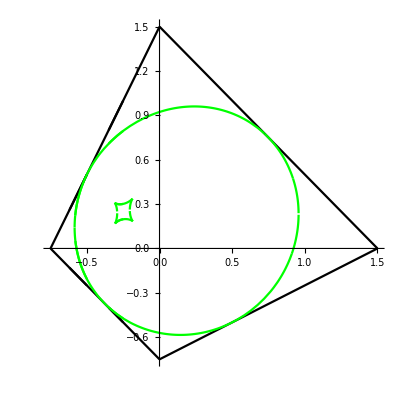

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/16)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Green}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/16)==0,v]},{u,-.35,-.25},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Green}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/16)==0,v]},{u,-.62,-.5},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Green}];
Plot5=Show[%,%%,%%%]
```

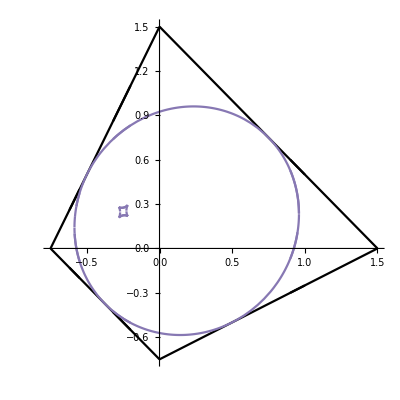

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/32)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Grey}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/32)==0,v]},{u,-.32,-.2},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Grey}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/32)==0,v]},{u,-.62,-.55},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Grey}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->1/2-1/32)==0,v]},{u,.9,1},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Grey}];
Plot6=Show[%,%%,%%%,%%%%]
```

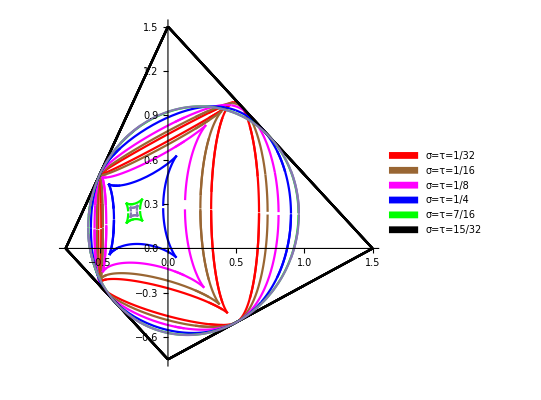

```mathematica
image=Show[Legended[Plot1,SwatchLegend[{Red},{"σ=τ=1/32"}]],Legended[Plot2,SwatchLegend[{Brown},{"σ=τ=1/16"}]],Legended[Plot3,SwatchLegend[{Magenta},{"σ=τ=1/8"}]],
Legended[Plot4,SwatchLegend[{Blue},{"σ=τ=1/4"}]],Legended[Plot5,SwatchLegend[{Green},{"σ=τ=7/16"}]],
Legended[Plot6,SwatchLegend[{Grey},{"σ=τ=15/32"}]]
]
```

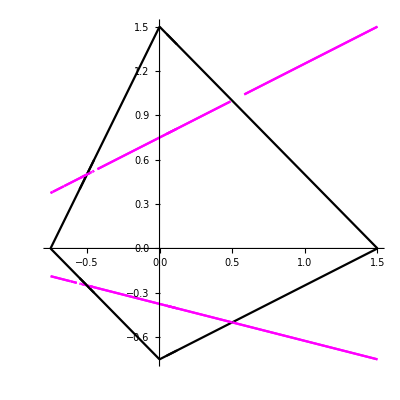

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->0)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->0)==0,v]},{u,-.55,-.45},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve/.σ->0)==0,v]},{u,.05,.12},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot0=Show[%,%%,%%%]
```

```mathematica
case τ=1-σ
Evolution (σ,1-σ) for σ in [1/2,1]
```

```mathematica
curve1=-6561-17496 u+34992 u^2+62208 u^3-82944 u^4-17496 v-34992 u v+46656 u^2 v+41472 u^3 v+34992 v^2+116640 u v^2-264384 u^2 v^2-497664 u^3 v^2+663552 u^4 v^2+132192 v^3+274752 u v^3-373248 u^2 v^3-331776 u^3 v^3+33696 v^4-93312 u v^4+435456 u^2 v^4+995328 u^3 v^4-1327104 u^4 v^4-217728 v^5-518400 u v^5+746496 u^2 v^5+663552 u^3 v^5-269568 v^6-373248 u v^6+248832 u^2 v^6-124416 v^7-82944 u v^7-20736 v^8+78732 σ+131220 u σ-303264 u^2 σ-699840 u^3 σ+663552 u^4 σ+774144 u^5 σ-589824 u^6 σ+288684 v σ+705672 u v σ-886464 u^2 v σ-2788992 u^3 v σ+1548288 u^4 v σ+3317760 u^5 v σ-2359296 u^6 v σ+64152 v^2 σ+1271376 u v^2 σ+62208 u^2 v^2 σ-2916864 u^3 v^2 σ-442368 u^4 v^2 σ+3981312 u^5 v^2 σ-2359296 u^6 v^2 σ-431568 v^3 σ+438048 u v^3 σ+898560 u^2 v^3 σ-1207296 u^3 v^3 σ+884736 u^4 v^3 σ+884736 u^5 v^3 σ+702432 v^4 σ-986688 u v^4 σ-1866240 u^2 v^4 σ-3087360 u^3 v^4 σ+5308416 u^4 v^4 σ+1982016 v^5 σ+667008 u v^5 σ-3566592 u^2 v^5 σ-2451456 u^3 v^5 σ+637056 v^6 σ+3518208 u v^6 σ-2433024 u^2 v^6 σ-624384 v^7 σ+1783296 u v^7 σ-299520 v^8 σ-314928 σ^2-131220 u σ^2+1280124 u^2 σ^2+1143072 u^3 σ^2-1975104 u^4 σ^2-1520640 u^5 σ^2+1437696 u^6 σ^2-1548396 v σ^2-2006208 u v σ^2+5727024 u^2 v σ^2+8164800 u^3 v σ^2-8847360 u^4 v σ^2-9234432 u^5 v σ^2+8110080 u^6 v σ^2-2026620 v^2 σ^2-7406640 u v^2 σ^2+7103376 u^2 v^2 σ^2+16084224 u^3 v^2 σ^2-10630656 u^4 v^2 σ^2-8957952 u^5 v^2 σ^2+5750784 u^6 v^2 σ^2-23328 v^3 σ^2-8320320 u v^3 σ^2+1683072 u^2 v^3 σ^2+12510720 u^3 v^3 σ^2-7520256 u^4 v^3 σ^2-221184 u^5 v^3 σ^2-244944 v^4 σ^2+3329856 u v^4 σ^2-603072 u^2 v^4 σ^2+6584832 u^3 v^4 σ^2-8156160 u^4 v^4 σ^2-2655936 v^5 σ^2+6289920 u v^5 σ^2-601344 u^2 v^5 σ^2+4230144 u^3 v^5 σ^2-793152 v^6 σ^2-6296832 u v^6 σ^2+587520 u^2 v^6 σ^2+1419264 v^7 σ^2-5170176 u v^7 σ^2+656640 v^8 σ^2+262440 σ^3-1189728 u σ^3-1965384 u^2 σ^3+3506976 u^3 σ^3+1648512 u^4 σ^3-5571072 u^5 σ^3+1216512 u^6 σ^3+3932160 u^7 σ^3-2097152 u^8 σ^3+2589408 v σ^3-2881008 u v σ^3-12830400 u^2 v σ^3+6422976 u^3 v σ^3+15026688 u^4 v σ^3-5833728 u^5 v σ^3-5652480 u^6 v σ^3+2097152 u^7 v σ^3+6852600 v^2 σ^3+4548960 u v^2 σ^3-19152288 u^2 v^2 σ^3-1195776 u^3 v^2 σ^3+16533504 u^4 v^2 σ^3-5289984 u^5 v^2 σ^3+2179072 u^6 v^2 σ^3+4090176 v^3 σ^3+16765056 u v^3 σ^3-2958336 u^2 v^3 σ^3-7838208 u^3 v^3 σ^3-780288 u^4 v^3 σ^3-6516736 u^5 v^3 σ^3-7177248 v^4 σ^3+5011200 u v^4 σ^3+3839616 u^2 v^4 σ^3+35328 u^3 v^4 σ^3-7804928 u^4 v^4 σ^3-7105536 v^5 σ^3-10651392 u v^5 σ^3+2423808 u^2 v^5 σ^3-1586176 u^3 v^5 σ^3+4475520 v^6 σ^3+222720 u v^6 σ^3+7787008 u^2 v^6 σ^3+2909184 v^7 σ^3+3313664 u v^7 σ^3-2756096 v^8 σ^3+1338444 σ^4+3569184 u σ^4-2452356 u^2 σ^4-10380960 u^3 σ^4+7029504 u^4 σ^4+15019776 u^5 σ^4-10091520 u^6 σ^4-7888896 u^7 σ^4+5111808 u^8 σ^4+3569184 v σ^4+17455176 u v σ^4+3347568 u^2 v σ^4-40357440 u^3 v σ^4-141696 u^4 v σ^4+36799488 u^5 v σ^4-11169792 u^6 v σ^4-4964352 u^7 v σ^4-2452356 v^2 σ^4+23351328 u v^2 σ^4+12888720 u^2 v^2 σ^4-53129088 u^3 v^2 σ^4+2847744 u^4 v^2 σ^4+25740288 u^5 v^2 σ^4-18001920 u^6 v^2 σ^4-10532592 v^3 σ^4-7270560 u v^3 σ^4-3393792 u^2 v^3 σ^4-27862272 u^3 v^3 σ^4+23910912 u^4 v^3 σ^4+10776576 u^5 v^3 σ^4+6776784 v^4 σ^4-25522560 u v^4 σ^4-2096064 u^2 v^4 σ^4-15482880 u^3 v^4 σ^4+25073664 u^4 v^4 σ^4+20525184 v^5 σ^4+2443392 u v^5 σ^4+15061248 u^2 v^5 σ^4-1554432 u^3 v^5 σ^4-4473792 v^6 σ^4+14920704 u v^6 σ^4-6963456 u^2 v^6 σ^4-10513152 v^7 σ^4+4781568 u v^7 σ^4+3819264 v^8 σ^4-3149280 σ^5-1469664 u σ^5+11629008 u^2 σ^5+1096416 u^3 σ^5-21617280 u^4 σ^5+428544 u^5 σ^5+15399936 u^6 σ^5-2727936 u^7 σ^5-1572864 u^8 σ^5-15326496 v σ^5-19152288 u v σ^5+29229984 u^2 v σ^5+24183360 u^3 v σ^5-30951936 u^4 v σ^5-15856128 u^5 v σ^5+14764032 u^6 v σ^5+1867776 u^7 v σ^5-20703600 v^2 σ^5-45606240 u v^2 σ^5+12877056 u^2 v^2 σ^5+36695808 u^3 v^2 σ^5-6994944 u^4 v^2 σ^5+7160832 u^5 v^2 σ^5+5578752 u^6 v^2 σ^5+6881760 v^3 σ^5-19051200 u v^3 σ^5-3739392 u^2 v^3 σ^5+20915712 u^3 v^3 σ^5-2608128 u^4 v^3 σ^5+2936832 u^5 v^3 σ^5+23950080 v^4 σ^5+21862656 u v^4 σ^5+7596288 u^2 v^4 σ^5+15469056 u^3 v^4 σ^5+6610944 u^4 v^4 σ^5-7098624 v^5 σ^5-4631040 u v^5 σ^5-18178560 u^2 v^5 σ^5-1754112 u^3 v^5 σ^5-15572736 v^6 σ^5-21321216 u v^6 σ^5-13737984 u^2 v^6 σ^5+4603392 v^7 σ^5-2638848 u v^7 σ^5+3532800 v^8 σ^5-8188128 u σ^6-9996048 u^2 σ^6+21298464 u^3 σ^6+18449856 u^4 σ^6-24696576 u^5 σ^6-5688576 u^6 σ^6+14149632 u^7 σ^6-4870144 u^8 σ^6+8188128 v σ^6-12013920 u v σ^6-39680928 u^2 v σ^6+35308224 u^3 v σ^6+42550272 u^4 v σ^6-24551424 u^5 v σ^6-872448 u^6 v σ^6+1662976 u^7 v σ^6+28215216 v^2 σ^6+28063584 u v^2 σ^6-16765056 u^2 v^2 σ^6+36702720 u^3 v^2 σ^6-3628800 u^4 v^2 σ^6-40522752 u^5 v^2 σ^6+20455424 u^6 v^2 σ^6+15139872 v^3 σ^6+53037504 u v^3 σ^6+35209728 u^2 v^3 σ^6+28643328 u^3 v^3 σ^6-22333440 u^4 v^3 σ^6-11620352 u^5 v^3 σ^6-34271424 v^4 σ^6+8771328 u v^4 σ^6-12358656 u^2 v^4 σ^6-7306752 u^3 v^4 σ^6-45942784 u^4 v^4 σ^6-23390208 v^5 σ^6-2944512 u v^5 σ^6-11284992 u^2 v^5 σ^6+904192 u^3 v^5 σ^6+22823424 v^6 σ^6+8348160 u v^6 σ^6+25874432 u^2 v^6 σ^6+9159168 v^7 σ^6-4502528 u v^7 σ^6-9072640 v^8 σ^6+6298560 σ^7+14276736 u σ^7-7138368 u^2 σ^7-25940736 u^3 σ^7+8926848 u^4 σ^7+18786816 u^5 σ^7-10796544 u^6 σ^7-5566464 u^7 σ^7+4055040 u^8 σ^7+19315584 v σ^7+47869056 u v σ^7+7464960 u^2 v σ^7-47029248 u^3 v σ^7-18413568 u^4 v σ^7+4257792 u^5 v σ^7-4276224 u^6 v σ^7+2211840 u^7 v σ^7+4618944 v^2 σ^7+22208256 u v^2 σ^7+373248 u^2 v^2 σ^7-35458560 u^3 v^2 σ^7-1479168 u^4 v^2 σ^7-2598912 u^5 v^2 σ^7-14008320 u^6 v^2 σ^7-31352832 v^3 σ^7-57604608 u v^3 σ^7-49144320 u^2 v^3 σ^7-39730176 u^3 v^3 σ^7-15446016 u^4 v^3 σ^7-7372800 u^5 v^3 σ^7-13156992 v^4 σ^7-25132032 u v^4 σ^7+3138048 u^2 v^4 σ^7+12791808 u^3 v^4 σ^7+18247680 u^4 v^4 σ^7+25754112 v^5 σ^7+33481728 u v^5 σ^7+40366080 u^2 v^5 σ^7+12238848 u^3 v^5 σ^7+7147008 v^6 σ^7+6875136 u v^6 σ^7-3465216 u^2 v^6 σ^7-9142272 v^7 σ^7-884736 u v^7 σ^7+1363968 v^8 σ^7-5353776 σ^8-4199040 u σ^8+16971120 u^2 σ^8+5435424 u^3 σ^8-26158464 u^4 σ^8-248832 u^5 σ^8+14231808 u^6 σ^8-4663296 u^7 σ^8+479232 u^8 σ^8-24354432 v σ^8-40800672 u v σ^8+8561376 u^2 v σ^8+7262784 u^3 v σ^8-6811776 u^4 v σ^8+21247488 u^5 v σ^8+903168 u^6 v σ^8-4202496 u^7 v σ^8-30058128 v^2 σ^8-64688544 u v^2 σ^8-28180224 u^2 v^2 σ^8-22301568 u^3 v^2 σ^8+2951424 u^4 v^2 σ^8+34200576 u^5 v^2 σ^8-4460544 u^6 v^2 σ^8+12807072 v^3 σ^8+1975104 u v^3 σ^8+4883328 u^2 v^3 σ^8+12116736 u^3 v^3 σ^8+39817728 u^4 v^3 σ^8+17768448 u^5 v^3 σ^8+38382336 v^4 σ^8+17076096 u v^4 σ^8+6815232 u^2 v^4 σ^8-8672256 u^3 v^4 σ^8+19491840 u^4 v^4 σ^8-3545856 v^5 σ^8-31760640 u v^5 σ^8-31408128 u^2 v^5 σ^8-14008320 u^3 v^5 σ^8-22394880 v^6 σ^8-10469376 u v^6 σ^8-16054272 u^2 v^6 σ^8+1082880 v^7 σ^8+5529600 u v^7 σ^8+5630976 v^8 σ^8-2099520 σ^9-11897280 u σ^9-11150784 u^2 σ^9+13701312 u^3 σ^9+16578432 u^4 σ^9-3953664 u^5 σ^9-3050496 u^6 σ^9+2211840 u^7 σ^9-2211840 u^8 σ^9+699840 v σ^9-1306368 u v σ^9+3312576 u^2 v σ^9+21244032 u^3 v σ^9+7229952 u^4 v σ^9-6815232 u^5 v σ^9+1935360 u^6 v σ^9+18242496 v^2 σ^9+57900096 u v^2 σ^9+67651200 u^2 v^2 σ^9+48301056 u^3 v^2 σ^9+6414336 u^4 v^2 σ^9-5944320 u^5 v^2 σ^9+7741440 u^6 v^2 σ^9+17900352 v^3 σ^9+53903232 u v^3 σ^9+47056896 u^2 v^3 σ^9+10404864 u^3 v^3 σ^9-11197440 u^4 v^3 σ^9-3317760 u^5 v^3 σ^9-9082368 v^4 σ^9-2101248 u v^4 σ^9-7271424 u^2 v^4 σ^9-9123840 u^3 v^4 σ^9-16035840 u^4 v^4 σ^9-12040704 v^5 σ^9-4326912 u v^5 σ^9-2211840 u^2 v^5 σ^9+3170304 v^6 σ^9+4008960 u v^6 σ^9+8847360 u^2 v^6 σ^9+2626560 v^7 σ^9-1105920 u v^7 σ^9-2764800 v^8 σ^9+5038848 σ^10+14696640 u σ^10+5925312 u^2 σ^10-10404288 u^3 σ^10-3053376 u^4 σ^10-988416 u^5 σ^10-5213952 u^6 σ^10+1382400 u^7 σ^10+1658880 u^8 σ^10+12177216 v σ^10+26127360 u v σ^10+5085504 u^2 v σ^10-8263296 u^3 v σ^10-670464 u^4 v σ^10-9068544 u^5 v σ^10-2211840 u^6 v σ^10+2433024 u^7 v σ^10+46656 v^2 σ^10-14043456 u v^2 σ^10-35769600 u^2 v^2 σ^10-22159872 u^3 v^2 σ^10-8232192 u^4 v^2 σ^10-15234048 u^5 v^2 σ^10-3981312 u^6 v^2 σ^10-19455552 v^3 σ^10-42166656 u v^3 σ^10-36509184 u^2 v^3 σ^10-9197568 u^3 v^3 σ^10-10533888 u^4 v^3 σ^10-6635520 u^5 v^3 σ^10-11606976 v^4 σ^10-4278528 u v^4 σ^10+4845312 u^2 v^4 σ^10+14598144 u^3 v^4 σ^10+3207168 u^4 v^4 σ^10+9752832 v^5 σ^10+18413568 u v^5 σ^10+16865280 u^2 v^5 σ^10+7299072 u^3 v^5 σ^10+8748288 v^6 σ^10+1022976 u v^6 σ^10+663552 u^2 v^6 σ^10-2350080 v^7 σ^10-2211840 u v^7 σ^10-663552 v^8 σ^10-2519424 σ^11-6718464 u σ^11-5412096 u^2 σ^11-2612736 u^3 σ^11-1275264 u^4 σ^11+4492800 u^5 σ^11+4686336 u^6 σ^11-995328 u^7 σ^11-663552 u^8 σ^11-6718464 v σ^11-20901888 u v σ^11-23514624 u^2 v σ^11-15925248 u^3 v σ^11-926208 u^4 v σ^11+8709120 u^5 v σ^11+995328 u^6 v σ^11-1327104 u^7 v σ^11-5412096 v^2 σ^11-19035648 u v^2 σ^11-21835008 u^2 v^2 σ^11-12303360 u^3 v^2 σ^11+2280960 u^4 v^2 σ^11+8957952 u^5 v^2 σ^11+1327104 u^6 v^2 σ^11+1866240 v^3 σ^11-995328 u v^3 σ^11-4340736 u^2 v^3 σ^11-2156544 u^3 v^3 σ^11+6967296 u^4 v^3 σ^11+3981312 u^5 v^3 σ^11+6189696 v^4 σ^11+2059776 u v^4 σ^11-3359232 u^2 v^4 σ^11-6967296 u^3 v^4 σ^11-483840 v^5 σ^11-6552576 u v^5 σ^11-8957952 u^2 v^5 σ^11-3981312 u^3 v^5 σ^11-3608064 v^6 σ^11-995328 u v^6 σ^11-1327104 u^2 v^6 σ^11+995328 v^7 σ^11+1327104 u v^7 σ^11+663552 v^8 σ^11+419904 σ^12+1119744 u σ^12+3732480 u^2 σ^12+6096384 u^3 σ^12+1156032 u^4 σ^12-3684096 u^5 σ^12-2039040 u^6 σ^12+165888 u^7 σ^12+110592 u^8 σ^12+1119744 v σ^12+9144576 u v σ^12+20901888 u^2 v σ^12+17750016 u^3 v σ^12+573696 u^4 v σ^12-3967488 u^5 v σ^12-165888 u^6 v σ^12+221184 u^7 v σ^12+3732480 v^2 σ^12+20155392 u v^2 σ^12+31943808 u^2 v^2 σ^12+17985024 u^3 v^2 σ^12+877824 u^4 v^2 σ^12-1492992 u^5 v^2 σ^12-221184 u^6 v^2 σ^12+5349888 v^3 σ^12+15261696 u v^3 σ^12+16657920 u^2 v^3 σ^12+5391360 u^3 v^3 σ^12-1161216 u^4 v^3 σ^12-663552 u^5 v^3 σ^12-88128 v^4 σ^12+76032 u v^4 σ^12+1817856 u^2 v^4 σ^12+1161216 u^3 v^4 σ^12-2854656 v^5 σ^12-1423872 u v^5 σ^12+1492992 u^2 v^5 σ^12+663552 u^3 v^5 σ^12-656640 v^6 σ^12+165888 u v^6 σ^12+221184 u^2 v^6 σ^12-165888 v^7 σ^12-221184 u v^7 σ^12-110592 v^8 σ^12-1306368 u^2 σ^13-2612736 u^3 σ^13-435456 u^4 σ^13+1354752 u^5 σ^13+580608 u^6 σ^13-2612736 u v σ^13-7838208 u^2 v σ^13-6967296 u^3 v σ^13-193536 u^4 v σ^13+1161216 u^5 v σ^13-1306368 v^2 σ^13-7838208 u v^2 σ^13-13063680 u^2 v^2 σ^13-7354368 u^3 v^2 σ^13-580608 u^4 v^2 σ^13-2612736 v^3 σ^13-6967296 u v^3 σ^13-7354368 u^2 v^3 σ^13-2322432 u^3 v^3 σ^13-435456 v^4 σ^13-193536 u v^4 σ^13-580608 u^2 v^4 σ^13+1354752 v^5 σ^13+1161216 u v^5 σ^13+580608 v^6 σ^13+186624 u^2 σ^14+373248 u^3 σ^14+62208 u^4 σ^14-193536 u^5 σ^14-82944 u^6 σ^14+373248 u v σ^14+1119744 u^2 v σ^14+995328 u^3 v σ^14+27648 u^4 v σ^14-165888 u^5 v σ^14+186624 v^2 σ^14+1119744 u v^2 σ^14+1866240 u^2 v^2 σ^14+1050624 u^3 v^2 σ^14+82944 u^4 v^2 σ^14+373248 v^3 σ^14+995328 u v^3 σ^14+1050624 u^2 v^3 σ^14+331776 u^3 v^3 σ^14+62208 v^4 σ^14+27648 u v^4 σ^14+82944 u^2 v^4 σ^14-193536 v^5 σ^14-165888 u v^5 σ^14-82944 v^6 σ^14;
```

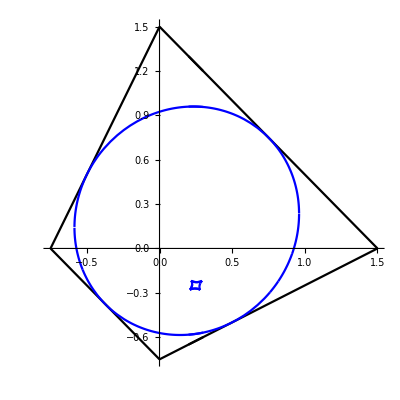

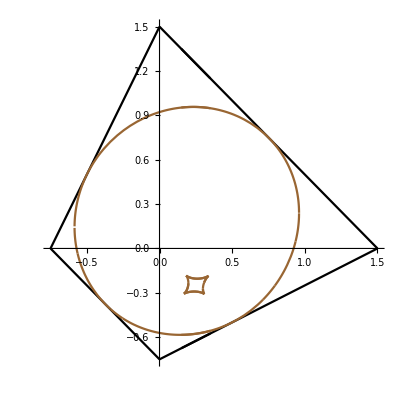

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/32)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Blue}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/32)==0,v]},{u,.2,.3},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Blue}];
Plot1=Show[%%,%]
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/16)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Brown}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/16)==0,v]},{u,.15,.35},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Brown}];
Plot2=Show[%,%%]
```

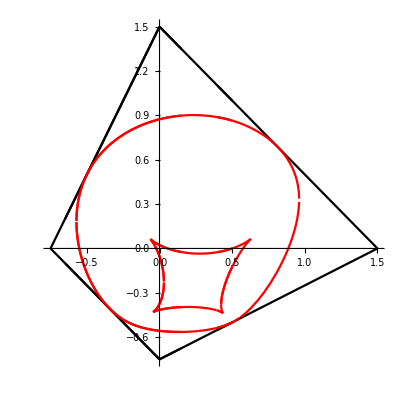

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/4)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/4)==0,v]},{u,-.65,.15},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1/2+1/4)==0,v]},{u,.4,.5},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Red}];
Plot3=Show[%,%%,%%%]
```

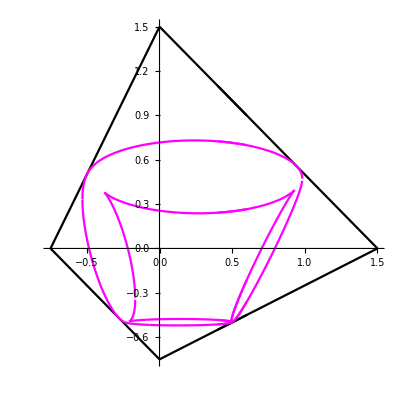

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1-1/16)==0,v]},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2,v/.NSolve[(curve1/.σ->1-1/16)==0,v]},{u,.4,.6},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Magenta}];
Plot4=Show[%,%%]
```

```mathematica
v/.NSolve[(curve1/.σ->0)==0,v]
```

{-0.5,-0.5,0.5,0.5,0.5 (-3.-8. u),0.5 (-3.-8. u),0.5 (-3.+4. u),0.5 (-3.+4. u)}

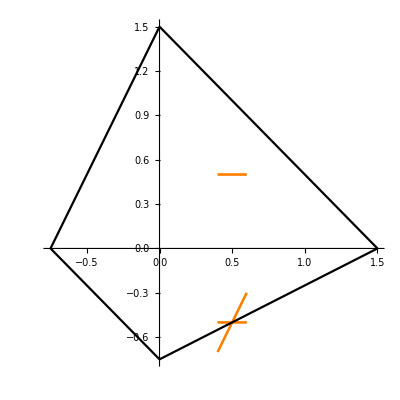

```mathematica
Plot[{-3/4-u,3/2-u,3/2+2 u,-3/4+u/2},su[1,1,3],PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Black,Black,Black,Black,Orange}];
Plot[{{-0.5,-0.5,0.5,0.5,0.5 (-3.-8. u),0.5 (-3.-8. u),0.5 (-3.+4. u),0.5 (-3.+4. u)}},{u,.4,.6},PlotRange->pr[1,1,3],AspectRatio->True,PlotStyle->{Orange}];
Plot5=Show[%,%%]
```

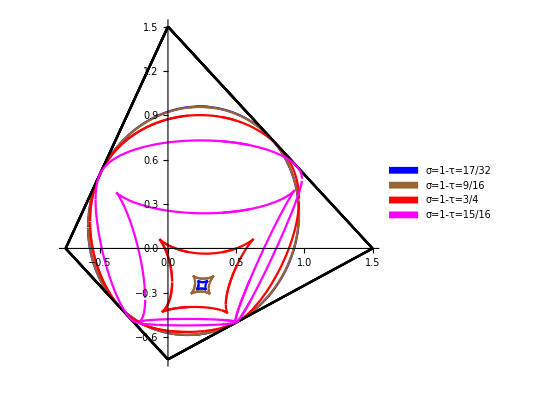

```mathematica
image=Show[Legended[Plot1,SwatchLegend[{Blue},{"σ=1-τ=17/32"}]],Legended[Plot2,SwatchLegend[{Brown},{"σ=1-τ=9/16"}]],Legended[Plot3,SwatchLegend[{Red},{"σ=1-τ=3/4"}]],
Legended[Plot4,SwatchLegend[{Magenta},{"σ=1-τ=15/16"}]](*Legended[Plot5,SwatchLegend[{Green},{"σ=τ=7/16"}]],
Legended[Plot6,SwatchLegend[{Grey},{"σ=τ=15/32"}]]*)
]
```